## Modelo contínuo do sistema

```mathematica
tf = TransferFunctionModel[(9080s+1.377*10^5)/(s^2+31.76s+213.1),s]
```

((137700.+9080. s)/(213.1+31.76 s+s^2))_^𝒯

```mathematica
ss = StateSpaceModel[tf]
```

(0 | 1. | 0
-213.1 | -31.76 | 1.
137700. | 9080. | 0)_^𝒮

## Modelo discreto do sistema

```mathematica
SSd = ToDiscreteTimeModel[ss,Ts,Method->"ForwardRectangularRule"]
```

(1 | 1. Ts | 0
-213.1 Ts | 1-31.76 Ts | 1. Ts
137700. | 9080. | 0)_Ts^𝒮

## Analisando a estabilidade do sistema

```mathematica
roots = Solve[TransferFunctionModel[SSd][[1]][[2]]==0,z ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.02 (50.-1106.55 Ts)},{z→0.02 (50.-481.452 Ts)}}

### Primeiro pólo do sistema em função do sampling time

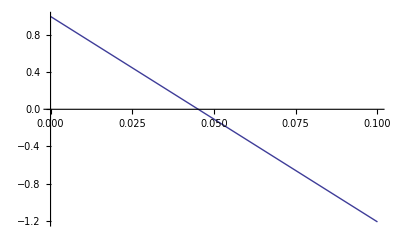

```mathematica
Plot[z/.(roots)[[1]],{Ts,0,0.1}]
```

### Segundo pólo do sistema em função do sampling time

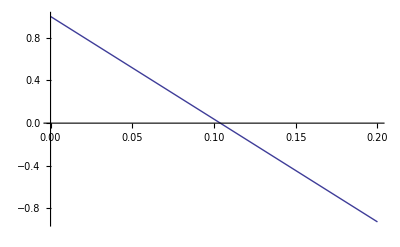

```mathematica
Plot[z/.(roots)[[2]],{Ts,0,0.2}]
```